```mathematica
mean12 := (Abs[Cos[x]]+Abs[Sin[x]])/2
```

```mathematica
var12 := (Abs[Cos[x]]-mean12)^2+(Abs[Sin[x]]-mean12)^2
```

```mathematica
Simplify[var12]
```

1/2 (Abs[Cos[x]]-Abs[Sin[x]])^2

```mathematica
m31:={{Cos[t1],-Sin[t1],0},{Sin[t1],Cos[t1],0},{0,0,1}}
```

```mathematica
MatrixForm[m31]
```

(Cos[t1] | -Sin[t1] | 0
Sin[t1] | Cos[t1] | 0
0 | 0 | 1)

```mathematica
m32:={{1,0,0},{0,Cos[t2],-Sin[t2]},{0,Sin[t2],Cos[t2]}}
```

```mathematica
m33:={{Cos[t3],0,Sin[t3]},{0,1,0},{-Sin[t3],0,Cos[t3]}}
```

```mathematica
m3:=m31.m32.m33
```

```mathematica
MatrixForm[m3]
```

(Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3] | -Cos[t2] Sin[t1] | Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3]
Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3] | Cos[t1] Cos[t2] | -Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3]
-Cos[t2] Sin[t3] | Sin[t2] | Cos[t2] Cos[t3])

```mathematica
mean13:=(Abs[m3[[1,1]]]+Abs[m3[[2,1]]]+Abs[m3[[3,1]]])/3
```

```mathematica
mean13
```

1/3 (Abs[Cos[t2] Sin[t3]]+Abs[Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]]+Abs[Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]])

```mathematica
var13:=(Abs[m3[[1,1]]] - mean13)^2+(Abs[m3[[2,1]]]-mean13)^2+(Abs[m3[[3,1]]]-mean13)^2
```

```mathematica
Simplify[Expand[var13]]
```

2/3 (Abs[Cos[t2] Sin[t3]]^2+Abs[Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]]^2-Abs[Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]] Abs[Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]]+Abs[Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]]^2-Abs[Cos[t2] Sin[t3]] (Abs[Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]]+Abs[Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]]))

```mathematica
t2:=0
```

```mathematica
Plot3D[var13,{t1,-Pi/2,Pi/2},{t3,-Pi/2,Pi/2}]
```

-Graphics3D-

```mathematica
Clear[t1,t2,t3]
```

```mathematica
FindMinimum[var13,{t1,t2,t3}]
```

{6.16298×10^-32,{t1→1.22652,t2→0.907152,t3→1.21471}}

```mathematica
m3/.FindMinimum[var13,{t1,t2,t3}][[2]]
```

{{-0.57735,-0.579846,0.574844},{0.57735,0.207907,0.789583},{-0.57735,0.787752,0.214739}}

```mathematica
1/(mean13/.FindMinimum[var13,{t1,t2,t3}][[2]])
```

1.73205

```mathematica
mean23:=(Abs[m3[[1,1]]]+Abs[m3[[2,1]]]+Abs[m3[[3,1]]]+Abs[m3[[1,2]]]+Abs[m3[[2,2]]]+Abs[m3[[3,2]]])/3
```

```mathematica
mean23
```

1/3 (Abs[Cos[t1] Cos[t2]]+Abs[Cos[t2] Sin[t1]]+Abs[Sin[t2]]+Abs[Cos[t2] Sin[t3]]+Abs[Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]]+Abs[Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]])

```mathematica
var23:=(Abs[m3[[1,1]]]+Abs[m3[[1,2]]] - mean23)^2+(Abs[m3[[2,1]]]+Abs[m3[[2,2]]]-mean23)^2+(Abs[m3[[3,1]]]+Abs[m3[[3,2]]]-mean23)^2
```

```mathematica
Simplify[Expand[var23]]
```

2/3 (Abs[Cos[t1] Cos[t2]]^2+Abs[Cos[t2] Sin[t1]]^2+Abs[Sin[t2]]^2+2 Abs[Sin[t2]] Abs[Cos[t2] Sin[t3]]+Abs[Cos[t2] Sin[t3]]^2-Abs[Sin[t2]] Abs[Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]]-Abs[Cos[t2] Sin[t3]] Abs[Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]]+Abs[Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]]^2-Abs[Cos[t2] Sin[t1]] (Abs[Sin[t2]]+Abs[Cos[t2] Sin[t3]]+Abs[Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]]-2 Abs[Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]])-Abs[Sin[t2]] Abs[Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]]-Abs[Cos[t2] Sin[t3]] Abs[Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]]-Abs[Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]] Abs[Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]]+Abs[Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]]^2-Abs[Cos[t1] Cos[t2]] (Abs[Cos[t2] Sin[t1]]+Abs[Sin[t2]]+Abs[Cos[t2] Sin[t3]]-2 Abs[Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]]+Abs[Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]]))

```mathematica
Plot3D[var23/.t3->0.9961815048532641,{t1,-Pi/2,Pi/2},{t2,-Pi/2,Pi/2}]
```

-Graphics3D-

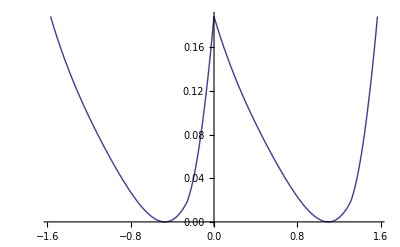

```mathematica
Plot[var23/.{t2->0.17116557968111068,t3->0.9961815048532641},{t1,-Pi/2,Pi/2}]
```

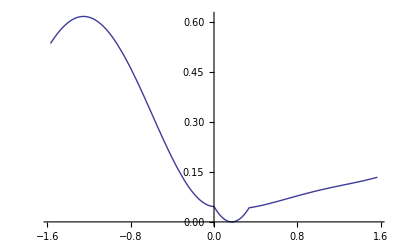

```mathematica
Plot[var23/.{t3->0.9961815048532641,t1->1.0983331072232845},{t2,-Pi/2,Pi/2}]
```

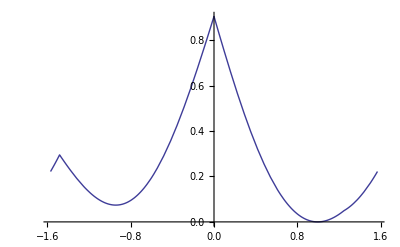

```mathematica
Plot[var23/.{t1->1.0983331072232845,t2->0.17116557968111068},{t3,-Pi/2,Pi/2}]
```

```mathematica
FindMinimum[var23,{t1,t2,t3}]
```

{5.23853×10^-32,{t1→1.3584,t2→-0.971876,t3→0.308737}}

```mathematica
m3/.FindMinimum[var23,{t1,t2,t3}][[2]]
```

{{0.446161,-0.551083,-0.705158},{0.878406,0.118838,0.462905},{-0.171299,-0.825945,0.537095}}

```mathematica
1/(mean23/.FindMinimum[var23,{t1,t2,t3}][[2]])
```

1.00276

```mathematica
Abs[m3[[1,1]]]+Abs[m3[[1,2]]]/.FindMinimum[var23,{t1,t2,t3}][[2]]
```

0.997244

```mathematica
Abs[m3[[2,1]]]+Abs[m3[[2,2]]]/.FindMinimum[var23,{t1,t2,t3}][[2]]
```

0.997244

```mathematica
Abs[m3[[3,1]]]+Abs[m3[[3,2]]]/.FindMinimum[var23,{t1,t2,t3}][[2]]
```

0.997244

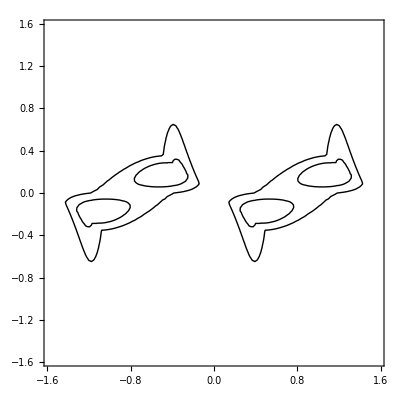

```mathematica
ContourPlot[var23/.t3->0.9961815048532641,{t1,-Pi/2,Pi/2},{t2,-Pi/2,Pi/2},Contours->{1/20,1/50},ContourShading->None,ContourStyle->Black]
```

```mathematica
max23:=Max[Abs[m3[[1,1]]]+Abs[m3[[1,2]]],Abs[m3[[2,1]]]+Abs[m3[[2,2]]],Abs[m3[[3,1]]]+Abs[m3[[3,2]]]]
```

```mathematica
Table[ContourPlot3D[Abs[m3[[n,1]]]+Abs[m3[[n,2]]]-mean23,{t1,-Pi/2,Pi/2},{t2,-Pi/2,Pi/2},{t3,-Pi/2,Pi/2},Contours->{0},Mesh->None],{n,{1,2,3}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
FindMinimum[var23,{{t1,0.23},{t2,0.23},{t3,-0.81}}]
```

{9.86076×10^-32,{t1→0.251299,t2→0.236684,t3→-0.819933}}

```mathematica
m3/.FindMinimum[var23,{{t1,0.23},{t2,0.23},{t3,-0.81}}][[2]]
```

{{0.703468,-0.24173,-0.668356},{0.00361126,0.941587,-0.336751},{0.710718,0.23448,0.663249}}

```mathematica
1/(mean23/.FindMinimum[var23,{{t1,0.23},{t2,0.23},{t3,-0.81}}][[2]])
```

1.05798

```mathematica
CForm[var23]
```

Power(Abs(Sin(t2)) + Abs(Cos(t2)*Sin(t3)) + (-Abs(Cos(t1)*Cos(t2)) - Abs(Cos(t2)*Sin(t1)) - Abs(Sin(t2)) - Abs(Cos(t2)*Sin(t3)) - 
        Abs(Cos(t3)*Sin(t1) + Cos(t1)*Sin(t2)*Sin(t3)) - Abs(Cos(t1)*Cos(t3) - Sin(t1)*Sin(t2)*Sin(t3)))/3.,2) + 
   Power(Abs(Cos(t1)*Cos(t2)) + Abs(Cos(t3)*Sin(t1) + Cos(t1)*Sin(t2)*Sin(t3)) + 
     (-Abs(Cos(t1)*Cos(t2)) - Abs(Cos(t2)*Sin(t1)) - Abs(Sin(t2)) - Abs(Cos(t2)*Sin(t3)) - Abs(Cos(t3)*Sin(t1) + Cos(t1)*Sin(t2)*Sin(t3)) - 
        Abs(Cos(t1)*Cos(t3) - Sin(t1)*Sin(t2)*Sin(t3)))/3.,2) + Power(Abs(Cos(t2)*Sin(t1)) + 
     (-Abs(Cos(t1)*Cos(t2)) - Abs(Cos(t2)*Sin(t1)) - Abs(Sin(t2)) - Abs(Cos(t2)*Sin(t3)) - Abs(Cos(t3)*Sin(t1) + Cos(t1)*Sin(t2)*Sin(t3)) - 
        Abs(Cos(t1)*Cos(t3) - Sin(t1)*Sin(t2)*Sin(t3)))/3. + Abs(Cos(t1)*Cos(t3) - Sin(t1)*Sin(t2)*Sin(t3)),2)